# Shallow Convolution Neural Network approach

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
files=FileNames["../datasets/Training/Happy/*.png",NotebookDirectory[]];
happyFaces =  ParallelMap[ Import, files];
```

```mathematica
files=FileNames["../datasets/Training/Neutral/*.png",NotebookDirectory[]];
neutralFaces =  ParallelMap[ Import, files];
```

```mathematica
files=FileNames["../datasets/Training/Sad/*.png",NotebookDirectory[]];
sadFaces =  ParallelMap[ Import, files];
```

```mathematica
files=FileNames["../datasets/Training/Angry/*.png",NotebookDirectory[]];
angryFaces =  ParallelMap[ Import, files]
```

$Aborted

```mathematica
files=FileNames["../datasets/Training/Surprise/*.png",NotebookDirectory[]];
surpriseFaces =  ParallelMap[ Import, files]
```

```mathematica
trainigDataset =  Join[
	<|"happy"->happyFaces|>,
	<|"neutral"->neutralFaces|>,
	<|"sad"->sadFaces|>,
    <|"angry"->angryFaces|>,
   <|"surprise"-> surpriseFaces |>
]
```

<|1|>
 |  |  |  |

```mathematica
trainData =   Reverse/@Flatten[Thread /@ Normal[trainigDataset]];
```

```mathematica
Export["/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/datasets/train.mx",trainData, "MX"]
```

/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/datasets/train.mx

/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/datasets/train.mx

```mathematica
emotionTypes = {"happy", "neutral","sad","angry","surprise"};
```

## Import test dataset

```mathematica
files=FileNames["../datasets/Test/Happy/*.png",NotebookDirectory[]];
happyFacesTest =   ParallelMap[ Import, files];
```

```mathematica
files=FileNames["../datasets/Test/Neutral/*.png",NotebookDirectory[]];
neutralFacesTest =   ParallelMap[ Import, files];
```

```mathematica
files=FileNames["../datasets/Test/Sad/*.png",NotebookDirectory[]];
sadFacesTest=  ParallelMap[ Import, files];
```

```mathematica
files=FileNames["../datasets/Test/Angry/*.png",NotebookDirectory[]];
angryFacesTest =   ParallelMap[ Import, files];
```

```mathematica
files=FileNames["../datasets/Test/Surprise/*.png",NotebookDirectory[]];
surpriseFacesTest =   ParallelMap[ Import, files];
```

```mathematica
testDataset =  Join[
	<|"happy"->  happyFacesTest |>,
	<|"neutral"-> neutralFacesTest|>,
	<|"sad"-> sadFacesTest|>,
  <|"angry"-> angryFacesTest|>,
  <|"surprise"->  surpriseFacesTest |>
];
```

```mathematica
testData =   Reverse/@Flatten[Thread /@ Normal[testDataset]];
```

```mathematica
Export["/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/datasets/test.mx",testData, "MX"]
```

/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/datasets/test.mx

```mathematica
imageDim = ImageDimensions[happyFaces[[1]]]
```

{48,48}

```mathematica
convNet=NetInitialize@NetChain[{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,Length[emotionTypes],DropoutLayer[0.2], SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",emotionTypes}],"Input"->NetEncoder[{"Image",imageDim,ColorSpace->"Grayscale"}]]
```

NetChain[]

```mathematica
NetGraph[convNet]
```

NetGraph[]

```mathematica
toPreserve ={ "TrainedNet",
	"BatchLossList",
    "RoundLossList",
	"ValidationLossList",
     "ValidationLossSeries",
          "LossEvolutionPlot",
     "RMSGradientLists",
          "RMSGradientEvolutionPlot",
     "RMSWeightLists","RMSWeightEvolutionPlot"};
```

```mathematica
lossFunction = CrossEntropyLossLayer["Index"]
```

CrossEntropyLossLayer[<>]

```mathematica
outputDir= "/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/models/shallow";
```

```mathematica
trainedConvNet=NetTrain[trainedConvNet[[1]],trainData, lossFunction,toPreserve,MaxTrainingRounds-> 10,
TrainingProgressCheckpointing->{"Directory",outputDir},
Method->{"ADAM"},
ValidationSet->testData,
BatchSize->64
]
```

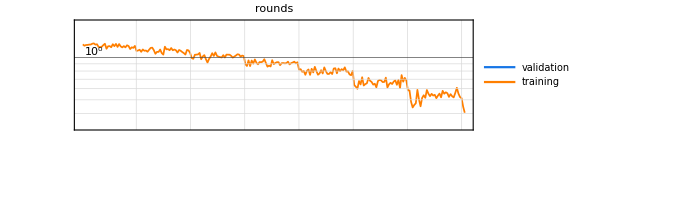

```mathematica
trainedConvNet[[6]]
```

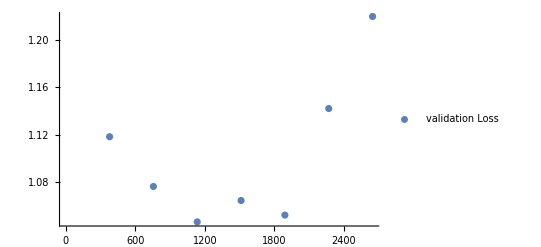

```mathematica
ListPlot[{trainedConvNet[[4]]},PlotLegends->{"validation Loss"} ]
```

```mathematica
net = Import["]
```

```mathematica
trainedConvNet[[8]]
```

-Graphics-

```mathematica
trainedConvNet[[10]]
```

-Graphics-

```mathematica
cnMeasurments = ClassifierMeasurements[trainedConvNet[[1]], testData]
```

ClassifierMeasurementsObject[…]

```mathematica
cnMeasurments[{"Accuracy",{"Accuracy"->2}, "AreaUnderROCCurve"}]
```

{0.582365,{0.780804},<|happy→0.902544,neutral→0.821521,sad→0.792151,angry→0.7959,surprise→0.928161|>}

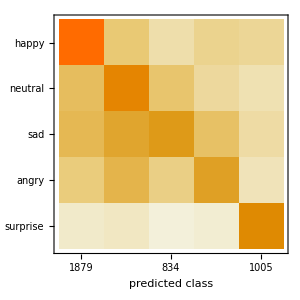

```mathematica
cnMeasurments["ConfusionMatrixPlot"]
```

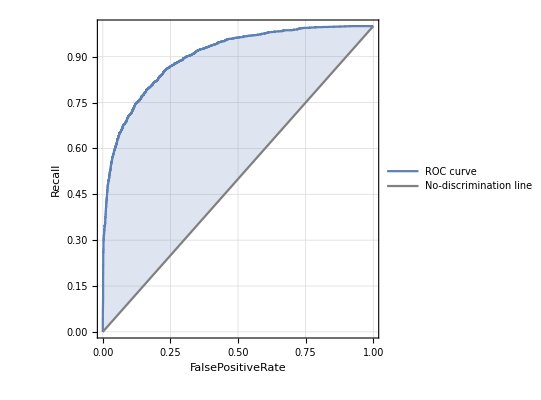
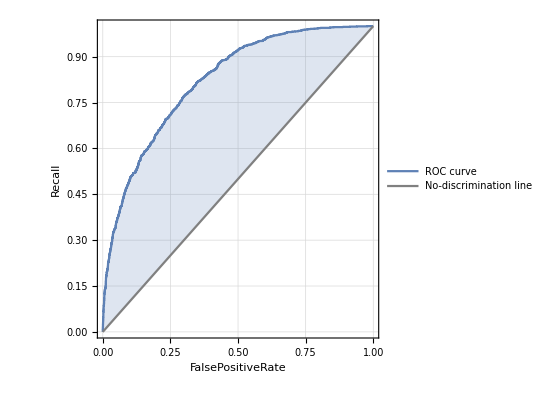
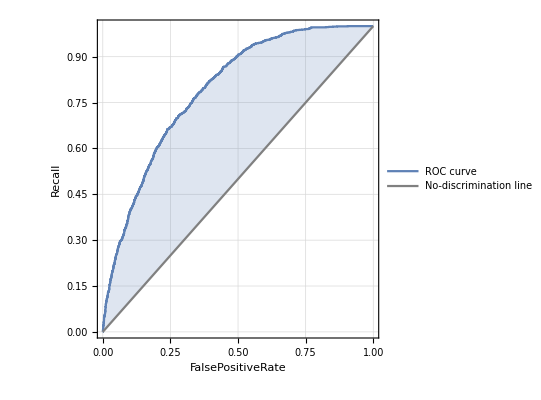
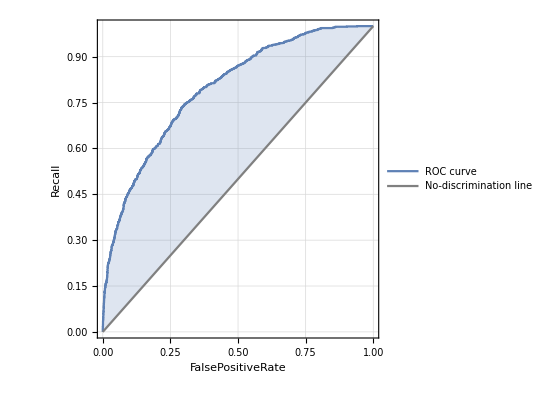
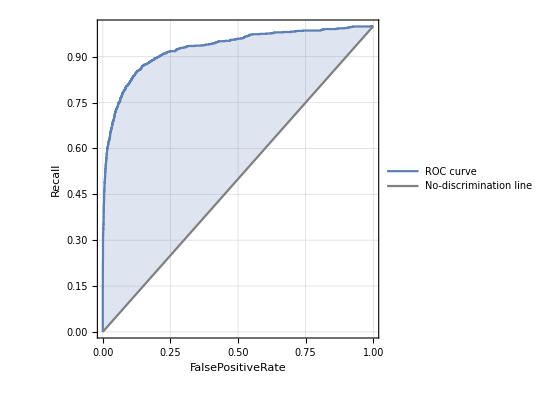
<|happy→-Graphics-,neutral→-Graphics-,sad→-Graphics-,angry→-Graphics-,surprise→-Graphics-|>

```mathematica
cnMeasurments["ROCCurve"]
```

```mathematica
cnMeasurments["TopConfusions"->3]
```

{sad→angry,neutral→sad,happy→neutral}

```mathematica
cnMeasurments["TruePositiveExamples"]
```

<|happy→{-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,1297,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy},3,surprise→1|>
 |  |  |  |

```mathematica
cnMeasurments["WorstClassifiedExamples"]
```

{-Graphics-→surprise,-Graphics-→neutral,-Graphics-→happy,-Graphics-→angry,-Graphics-→neutral,-Graphics-→happy,-Graphics-→sad,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→happy}

## Camera tests

```mathematica
trainedConvNet[[1]][{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{happy,neutral,happy,neutral,surprise,happy,neutral}

```mathematica
Dynamic[image=CurrentImage[];
box =  FindFaces[image];
face =   ImageTrim[image,#]&/@ box ;
face = face[[1]];
greyFace = ColorConvert[face,"Grayscale"];
Column[{image,greyFace,Column[trainedConvNet[[1]][greyFace,"TopProbabilities"]]}]]
```

```mathematica
greyFace = ColorConvert[face,"Grayscale"]
```

```mathematica
trainedNet = Import["/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/models/shallow/2017-06-27T14:50:04_1_04_1135_1.02e+0_1.05e+0.wlnet"]
```

NetChain[]

```mathematica
performanceBest = ClassifierMeasurements[trainedNet,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
performanceBest[{"Accuracy",{"Accuracy"->2}, "AreaUnderROCCurve"}]
```

{0.582365,{0.780804},<|happy→0.902544,neutral→0.821521,sad→0.792151,angry→0.7959,surprise→0.928161|>}